```mathematica
ClearAll["Global`*"]
```

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

C:\Users\fywen\Desktop\fyw\ndLSCOdat\TEST\admr_cdw_9x9

```mathematica
$HistoryLength=0;
```

# Define Band structure parameters & some useful constants

```mathematica
c=13.2; 
a =5.3/Sqrt[2];
b=5.3/Sqrt[2];
ℏ=1.05*10^-34;
e=1.6*10^-19;
m0=9.1*10^-31;
kB=1.38*10^-23;
jtoev=6.242*10^18; (*conversion constant from juole to eV*)
ty= 1.6*10^-22 * 1/(9.1*10^-31) 1/(10^-10)^2 10^-24;



v [f_]:=(9.1*10^-31)10^-20/(10^-12)*1/ℏ{D[f,kx],D[f,ky],D[f,kz]};
kf[F_]:=Sqrt[(F 2Pi (e/(1.6*10^-19))/(ℏ/(9.1*10^-31)*10^20) (1/10^-12))/Pi];
```

# Define tight-binding model dispersion

```mathematica
t=190*ty;
tp=-0.16*t;
tpp=0.07*t;
tz=0.035*t;
μ = 0.685*t;
ξ[kx_?NumericQ,ky_?NumericQ,mu_?NumericQ]:=-2t(Cos[kx a]+Cos[ky b])-2tp(Cos[kx a+ky b]+Cos[kx a- ky b])-2tpp(Cos[2kx a]+Cos[2ky b])+mu;
ξz[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=-2 tz*Cos[kz c/2](Cos [kx a ]-Cos[ky b])^2 Cos[(kx a )/2]Cos[(ky b )/2];


Q=2π/3/a;
(*here it could be functions of kx and ky like for dwave density waves*)
B=0(*-0.07*t*);
AA=0.1*t;

(*here it could be functions of kx and ky like for dwave density waves*)
tyQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);
txQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b] );
tsyQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);
tsxQ[kx_,ky_]:=AA-B*(Cos[kx a]-Cos[ky b]);

BDW2d[kx_,ky_,mu_]=({{ξ[kx,ky,mu], -tyQ[kx,ky+Q/2], -tyQ[kx,ky-Q/2], -txQ[kx+Q/2,ky], 0, 0, -txQ[kx-Q/2,ky], 0, 0}, {-tyQ[kx,ky+Q/2], ξ[kx,ky+Q,mu], -tyQ[kx,ky-3/2Q], 0, -tsxQ[kx+Q/2,ky+Q], 0, 0, -tsxQ[kx-Q/2,ky+Q], 0}, {-tyQ[kx,ky-Q/2], -tyQ[kx,ky+3/2Q], ξ[kx,ky+2Q,mu], 0, 0, -tsxQ[kx+Q/2,ky-Q], 0, 0, -tsxQ[kx-Q/2,ky-Q]}, {-txQ[kx+Q/2,ky], 0, 0, ξ[kx+Q,ky,mu], -tsyQ[kx+Q,ky+Q/2], -tsyQ[kx+Q,ky-Q/2], -txQ[kx-3/2Q,ky], 0, 0}, {0, -tsxQ[kx+Q/2,ky+Q], 0, -tsyQ[kx+Q,ky+Q/2], ξ[kx+Q,ky+Q,mu], -tsyQ[kx+Q,ky-3/2Q], 0, -tsxQ[kx-3/2Q,ky+Q], 0}, {0, 0, -tsxQ[kx+Q/2,ky-Q], -tsyQ[kx+Q,ky-Q/2], -tsyQ[kx+Q,3/2Q+ky], ξ[kx+Q,ky+2Q,mu], 0, 0, -tsxQ[kx-3/2Q,ky-Q]}, {-txQ[kx-Q/2,ky], 0, 0, -txQ[kx+3/2Q,ky], 0, 0, ξ[kx+2Q,ky,mu], -tsyQ[kx-Q,ky+Q/2], -tsyQ[kx-Q,ky-Q/2]}, {0, -tsxQ[kx-Q/2,ky+Q], 0, 0, -tsxQ[kx+3/2Q,ky+Q], 0, -tsyQ[kx-Q,ky+Q/2], ξ[kx+2Q,ky+Q,mu], -tsyQ[kx-Q,ky-3/2Q]}, {0, 0, -tsxQ[kx-Q/2,ky-Q], 0, 0, -tsxQ[kx+3/2Q,ky-Q], -tsyQ[kx-Q,ky-Q/2], -tsyQ[kx-Q,ky+3/2Q], ξ[kx+2Q,ky+2Q,mu]}});
BDWbands[kx_,ky_,mu_?NumericQ]:=BDWbands[kx,ky,mu]=Sort[Eigenvalues[BDW2d[kx,ky,mu]]];
```

# Calculationg of the doping of the un - reconstruced band

```mathematica
doping=0;
f[kx_?NumericQ,ky_?NumericQ]:=ξ[kx,ky,μ]
area=NIntegrate[Boole[f[kx,ky]>= 0],{kx,-Pi/a,Pi/a},{ky,-Pi/a,Pi/a}];
atotal= (2Pi/a)(2Pi/b);
per = area/atotal
doping=per*2-1
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.57156 and 0.000636844 for the integral and error estimates.

0.559105

0.118211

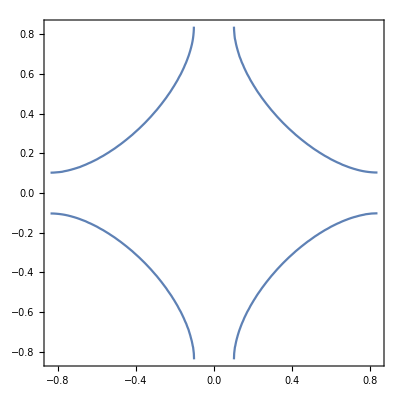

```mathematica
ContourPlot[ξ[x,y,μ](*+ξz[x,y,0]==*)==0,{x,-Pi/a,Pi/a},{y,-Pi/a,Pi/a}]
```

# BDW Spectral weight in the full brillouin zone It is faster to compute the spectral weight than a contour plot

```mathematica
SpectralWeight[x_]:=Blend[{{0,RGBColor[1,1,1]},{0.002,RGBColor[0.866,0.866,0.866]},{0.05,RGBColor[0,0,1,1]},{0.66,RGBColor[1,0.5,0,1]},{1,RGBColor[1,0,0,1]}},x];
```

```mathematica
ClearAll[A]
```

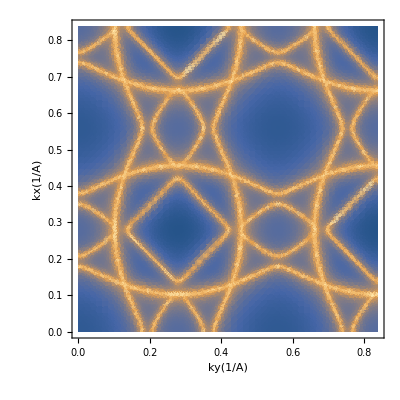

```mathematica
η=0.002*t;
A[kx_, ky_,mu_,ω_]:=Tr[Im[Inverse[((ω-I*η)*IdentityMatrix[9]- BDW2d[kx, ky,mu])]]
]/π;
Show[DensityPlot[Log[A[kx,ky,μ,0]],{ky,0,Pi/a},{kx,0,Pi/a},PlotPoints->50,PlotRange->Full,AspectRatio->1/1(*,ColorFunction->SpectralWeight*),Frame->True,FrameLabel->{{ Text[Style["kx(1/A)",FontSize->24,FontFamily->"Helvetica"]],None},{ Text[Style["ky(1/A)",FontSize->24,FontFamily->"Helvetica"]],None}}]]
```

BDW Energy contour of bands 3,4,5 in the full brillouin zone
The electron pocket is a portion of band 4. These 3 bands are the only that cross the Fermi Level

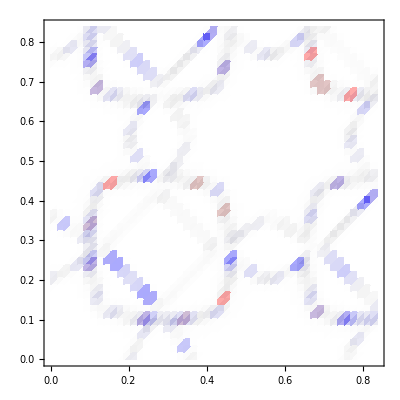

```mathematica
η=0.001*t;
A3[kx_, ky_,mu_,ω_]:=Im[1/((ω-I*η)- BDWbands[kx, ky,mu][[3]])]/π;
A4[kx_, ky_,kz_,mu_,ω_]:=Im[1/((ω-I*η)-( BDWbands[kx, ky,mu][[4]]+ξz[kx,ky,kz]))]/π;
A5[kx_, ky_,mu_,ω_]:=Im[1/((ω-I*η)- BDWbands[kx, ky,mu][[5]])]/π;

customColor[x_]:=Blend[{{0,RGBColor[1,1,1]},{0.002,RGBColor[0.866,0.866,0.866]},{0.05,RGBColor[0,0,1,1]},{0.66,RGBColor[1,0.5,0,1]},{1,RGBColor[1,0,0,1]}},x];
GraphicsRow[{
DensityPlot[A4[kx,ky,2Pi/c,μ,0],{ky,0,π/a},{kx,0,π/a},PlotPoints->50,PlotRange->Full,AspectRatio->1/1,ColorFunction->customColor]
},ImageSize->Medium]
```

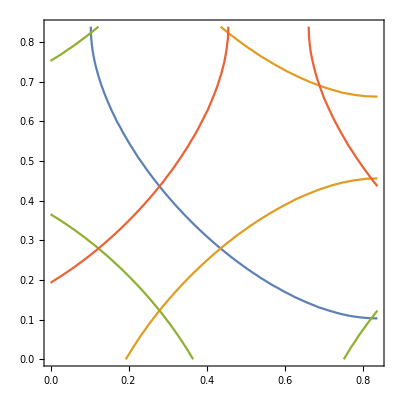

```mathematica
Show[ContourPlot[{ξ[kx,ky,μ]==0,ξ[kx,ky-Q,μ]==0,ξ[kx-Q,ky-Q,μ]==0,ξ[kx-Q,ky,μ]==0},{kx,0,Pi/a},{ky,0,Pi/a}],DensityPlot[A4[kx,ky,μ,0],{ky,0,π/a},{kx,0,π/a},PlotPoints->100,PlotRange->Full,AspectRatio->1/1,ColorFunction->customColor]]
```

```mathematica
Find a uniform grid of the Fermi surface
```

```mathematica
dist=1.0*0.595

UpperBx ={0.37*a,.663*a,1.58,(1.04+dist)};
LowerBx ={0.2*a,0.45*a,0.5,(1.04-dist)};
UpperBy ={1.14* 0.09*a,1.58,0.663*a,(1.04+dist)};
LowerBy ={-1.14* 0.09*a,0.5,0.45*a,(1.04-dist)};
centerx={Pi/3,Pi 2/3.,0.28*a,Pi/3};
centery={0,0.28*a,Pi 2/3.,Pi/3}
differy = UpperBy - LowerBy ;
differx = UpperBx - LowerBx ;
numb =100;(*initial grid size numb x numb*)
gridnum=56;
subnum = 4;
h = 10^-8;(*finite element step*)
cdev=6; (*number of z direction layer *)
refineNum =2; (*recursively refine the mesh*)
FSindex=4
```

0.595

{0,1.04935,2.0944,π/3}

4

# Build 2 D interpolated function

```mathematica
numb =100
EngInt[kx_?NumericQ,ky_?NumericQ]:=BDWbands[kx, ky,μ][[4]];  (*interpolation function CDW band *)
plot1=Flatten[Table[{kx,ky,EngInt[kx,ky]},{kx,(LowerBx[[FSindex]]-3*differx[[FSindex]]/numb)/a,(UpperBx[[FSindex]]+3*differx[[FSindex]]/numb)/a,differx[[FSindex]]/numb/a},{ky,(LowerBy[[FSindex]]-3*differx[[FSindex]]/numb)/a,(UpperBy[[FSindex]]+3*differx[[FSindex]]/numb)/a,differy[[FSindex]]/numb/a}],1];(*compute 2D interpolation grid*)
(*refineselect = Select[plot1,#[[3]]>-2*tz&&#[[3]]<2*tz &];*)
test =  Interpolation[plot1,InterpolationOrder->2];
func[x_,y_] := Piecewise[{{test[x,y],x>0 &&y>0},{test[x,-y],x>0 && y < 0},{test[-x,-y],x<0 && y < 0},{test[-x,y],x<0 && y > 0}}]
(*V[kx_,ky_,kz_]:= (9.1*10^-31)10^-20/(10^-12)*1/ℏ*{(eng[kx+h,ky,kz]-eng[kx,ky,kz])/h,(eng[kx,ky+h,kz]-eng[kx,ky,kz])/h,(eng[kx,ky,kz+h]-eng[kx,ky,kz])/h};*)
```

100

```mathematica
Show[ListPointPlot3D[plot1]]
```

-Graphics3D-

# Export grid (for testing general band structure )

```mathematica
Export["grid.dat",plot1,"Table"]
```

grid.dat

# For general band structure import the dispersion (E(kx,ky) on a regular grid)

```mathematica
testdat = Import["grid.dat","Table"];
test =  Interpolation[testdat,InterpolationOrder->2];
func[x_,y_] := Piecewise[{{test[x,y],x>0 &&y>0},{test[x,-y],x>0 && y < 0},{test[-x,-y],x<0 && y < 0},{test[-x,y],x<0 && y > 0}}]
```

```mathematica
Show[Plot3D[eng[x,y,0],{x,0.122,0.439},{y,0.436,0.119},PlotRange->All](*,ListPointPlot3D[plot1]*),Plot3D[{0},{x,0.122,0.439},{y,0.436,0.119},PlotStyle->Blue]]
```

-Graphics3D-

# Parameters for Finding Fermi surface with grid search algorithm

Algorithm description :
1. compute the E(kx,ky)

```mathematica
dist=1.0*0.58 (*starting from the center of the cdw diamond FS, the width of the*) 
UpperBx ={0.37*a,.663*a,1.58,(1.04+dist)};
LowerBx ={0.2*a,0.45*a,0.5,(1.04-dist)};
UpperBy ={1.14* 0.09*a,1.58,0.663*a,(1.04+dist)};
LowerBy ={-1.14* 0.09*a,0.5,0.45*a,(1.04-dist)};
centerx={Pi/3,Pi 2/3.,0.28*a,Pi/3};
centery={0,0.28*a,Pi 2/3.,Pi/3}
differy = UpperBy - LowerBy 
differx = UpperBx - LowerBx 
numb =50;
gridnum=56;
subnum = 4;
h = 10^-8;
cdev=6;
refineNum =2;
delta = 0.01*ty
eng[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];
(*V[kx_,ky_,kz_]:= (9.1*10^-31)10^-20/(10^-12)*1/ℏ*{(eng[kx+h,ky,kz]-eng[kx,ky,kz])/h,(eng[kx,ky+h,kz]-eng[kx,ky,kz])/h,(eng[kx,ky,kz+h]-eng[kx,ky,kz])/h};*)
```

0.58

{0,1.04935,2.0944,π/3}

{0.769021,1.08,0.798253,1.16}

{0.637103,0.798253,1.08,1.16}

175.824

```mathematica
start={};
circ={};
Block[{plot1,plot2,plot3,plot4,plotTot,ConOri,Con,plot1sub,plot2sub,plot3sub,plot4sub,plotTotsub,Bsort,diff,interpoY,interpoX,funcX,funcY,rowpoint, colpoint},
Do[
(*Initial mesh*)
zrang =Range[-2.*Pi/c+4.*Pi/c/cdev/2,2.*Pi/c,4.*Pi/c/cdev];

plot1=Table[Table[{kx,ky, If[eng[kx,ky,kz]>0,1,0]},{kx,(LowerBx[[FSindex]])/a,(UpperBx[[FSindex]])/a,differx[[FSindex]]/numb/a},{ky,LowerBy[[FSindex]]/a,UpperBy[[FSindex]]/a,differy[[FSindex]]/numb/a}],{kz,zrang}];
plotTot =Table[Flatten[Table[ Table[{1/4*(plot1[[k,j,i,1]]+plot1[[k,j+1,i,1]]+plot1[[k,j,i+1,1]]+plot1[[k,j+1,i+1,1]]),1/4*(plot1[[k,j,i,2]]+plot1[[k,j+1,i,2]]+plot1[[k,j,i+1,2]]+plot1[[k,j+1,i+1,2]]),If[(plot1[[k,j,i,3]]+plot1[[k,j+1,i,3]]+plot1[[k,j,i+1,3]]+plot1[[k,j+1,i+1,3]])<3.5,If[(plot1[[k,j,i,3]]+plot1[[k,j+1,i,3]]+plot1[[k,j,i+1,3]]+plot1[[k,j+1,i+1,3]])>0.5,1],0]},{i,1,Length[plot1[[k,j]]]-1}],{j,1,Length[plot1[[k]]]-1}],1],{k,1,Length[zrang]}];
ConOri = Table[Transpose[Transpose[Select[plotTot[[j]],If[FSindex==4,(#[[3]]==1&&Sqrt[(#[[1]]-1.05/a*1)^2+(#[[2]]-1.05/a*1)^2]<0.96dist/a),(#[[3]]==1)]&]][[{1,2}]]],{j,1,Length[zrang]}];
Con=ConOri;
cellsizeY=differy/numb/a;
cellsizeX=differx/numb/a;


(*Refine Mesh*)

Do[

plot1sub=Table[Table[Table[Table[{kx,ky, If[eng[kx,ky,zrang[[j]]]>0,1,0]},{kx,(Con[[j,i,1]]-cellsizeX[[FSindex]]/2),(Con[[j,i,1]]+cellsizeX[[FSindex]]/2),cellsizeX[[FSindex]]/subnum}],{ky,(Con[[j,i,2]]-cellsizeY[[FSindex]]/2),(Con[[j,i,2]]+cellsizeY[[FSindex]]/2),cellsizeY[[FSindex]]/subnum}],{i,1,Length[Con[[j]]]}],{j,1,Length[zrang]}];
plotTotsub =Table[ Flatten[Table[Table[Table[{1/4*(plot1sub[[kz,pi,j,i,1]]+plot1sub[[kz,pi,j+1,i,1]]+plot1sub[[kz,pi,j,i+1,1]]+plot1sub[[kz,pi,j+1,i+1,1]]),1/4*(plot1sub[[kz,pi,j,i,2]]+plot1sub[[kz,pi,j+1,i,2]]+plot1sub[[kz,pi,j,i+1,2]]+plot1sub[[kz,pi,j+1,i+1,2]]),If[(plot1sub[[kz,pi,j,i,3]]+plot1sub[[kz,pi,j+1,i,3]]+plot1sub[[kz,pi,j,i+1,3]]+plot1sub[[kz,pi,j+1,i+1,3]])<3.5,If[(plot1sub[[kz,pi,j,i,3]]+plot1sub[[kz,pi,j+1,i,3]]+plot1sub[[kz,pi,j,i+1,3]]+plot1sub[[kz,pi,j+1,i+1,3]])>0.5,1],0]},{i,1,Length[plot1sub[[kz,pi,j]]]-1}],{j,1,Length[plot1sub[[kz,pi]]]-1}],{pi,1,Length[plot1sub[[kz]]]}],2],{kz,1,Length[zrang]}];

Con = Table[Transpose[Transpose[Select[plotTotsub[[j]],(#[[3]]==1)&]][[{1,2}]]]
,{j,1,Length[zrang]}];
cellsizeY[[FSindex]]=cellsizeY[[FSindex]]/subnum;
cellsizeX[[FSindex]]=cellsizeX[[FSindex]]/subnum;
Print[Dimensions[Con[[1]]]]
,refineNum];
(*process grid-Marching square*)
rowpoint= Table[Flatten[Table[Table[Table[{1/2*(plot1sub[[kz,pi,j,i,1]]+plot1sub[[kz,pi,j+1,i,1]]),0.5*(plot1sub[[kz,pi,j,i,2]]+plot1sub[[kz,pi,j+1,i,2]]),If[Xor[plot1sub[[kz,pi,j,i,3]]>0.5,plot1sub[[kz,pi,j+1,i,3]]>0.5],1,0]},{i,1,Length[plot1sub[[kz,pi,j]]]}],{j,1,Length[plot1sub[[kz,pi]]]-1}],{pi,1,Length[plot1sub[[kz]]]}],2],{kz,1,Length[zrang]}];
colpoint= Table[Flatten[Table[Table[Table[{1/2*(plot1sub[[kz,pi,j,i,1]]+plot1sub[[kz,pi,j,i+1,1]]),0.5*(plot1sub[[kz,pi,j,i,2]]+plot1sub[[kz,pi,j,i+1,2]]),If[Xor[plot1sub[[kz,pi,j,i,3]]>0.5,plot1sub[[kz,pi,j,i+1,3]]>0.5],1,0]},{i,1,Length[plot1sub[[kz,pi,j]]]-1}],{j,1,Length[plot1sub[[kz,pi]]]}],{pi,1,Length[plot1sub[[kz]]]}],2],{kz,1,Length[zrang]}];
Con= Table[Transpose[Transpose[Join[Select[rowpoint[[j]],(#[[3]]==1)&],Select[colpoint[[j]],(#[[3]]==1)&]]][[{1,2}]]]
,{j,1,Length[zrang]}];

(*Get Fermi Surface*)
Bsort =  Table[Transpose[Transpose[SortBy[ Table[{Con[[j,i,1]],Con[[j,i,2]],ArcTan[Con[[j,i,1]]-centerx[[FSindex]]/a,Con[[j,i,2]]-centery[[FSindex]]/a]},{i,1,Length[Con[[j]]]}],Last]][[{1,2}]]],{j,1,Length[zrang]}];
diff =Table[Join[{0}, Accumulate[Table[Sqrt[(Bsort[[j,i,1]]-Bsort[[j,i+1,1]])^2+(Bsort[[j,i,2]]-Bsort[[j,i+1,2]])^2],{i,1,Length[Bsort[[j]]]-1}]]],{j,1,Length[zrang]}];
interpoX= Table[Transpose[{SetPrecision[diff[[j]],10],Bsort[[j,All,1]]}],{j,1,Length[zrang]}];
interpoY=  Table[Transpose[{SetPrecision[diff[[j]],10],Bsort[[j,All,2]]}],{j,1,Length[zrang]}];
funcX = Table[Interpolation[DeleteDuplicatesBy[interpoX[[j]],First],InterpolationOrder->1],{j,1,Length[zrang]}];
funcY = Table[Interpolation[DeleteDuplicatesBy[interpoY[[j]],First],InterpolationOrder->1],{j,1,Length[zrang]}];
start =Join[start,Flatten[{Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[Pi/2],-Sin[Pi/2],0},{Sin[Pi/2],Cos[Pi/2],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[Pi],-Sin[Pi],0},{Sin[Pi],Cos[Pi],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[3 Pi/2],-Sin[3Pi/2],0},{Sin[3Pi/2],Cos[3Pi/2],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1]},1]];
circ=Join[circ,Flatten[Table[Table[Table[diff[[j,Length[diff[[j]]]]]/gridnum,{i,1,gridnum(*phispecial*)}],{j,1,Length[zrang]}],{4}],2]];,{FSindex,{4}(*Length[UpperBx]*)}];
ClearSystemCache[];]
start01=start;
circ01=circ;
```

{720,2}

{2880,2}

```mathematica
ListPointPlot3D[start01]
```

-Graphics3D-

```mathematica
Calculate the ADMR
```

```mathematica
tdevs=800;(*number of time step for differential equation*)
θdevs=8; (*number of θ angle*)
θmax=100; (*maximum θ angle*)
θmin=0; (*minimum θ angle*)
thetas =(*{80.,100.}*Pi/180*) Table[θ,{θ,θmin*Pi/180,θmax*Pi/180.,(θmax-θmin)*Pi/180./θdevs}]; 
phis = {0.*Pi/180(*,15.*Pi/180,30.*Pi/180,45.*Pi/180*)}; (*phi angle list*)
param=Flatten[Table[{the,phi},{the,thetas},{phi,phis}],1] (*parameter list*)
hopping={{0.1}};(*tau*)
```

{{0.,0.},{0.218166,0.},{0.436332,0.},{0.654498,0.},{0.872665,0.},{1.09083,0.},{1.309,0.},{1.52716,0.},{1.74533,0.}}

```mathematica
Brange=(*Range[41,45,1]*){45}; (*magnetic field strength*)
tnum =8; (**)

numbTimes=1;
numGrid01=Length[start01];


(*velocityz01=velocity01[[3]];*)
 cond01= Table[Table[{0,0,0},{Length[thetas]}],{Length[phis]}];

(*start01= Drop[Import["FS_kx_ky_kz.dat","Table"],1];
 *)
Bfield=45*1.6*10^-19 * 10^-12/(9.1*10^-31);
(*efun=Compile[{{kx,_Real},{ky,_Real},{kz,_Real}},inplanFermi[kx,ky]+ξz[kx,ky,kz]];*)
efun01[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];


h=10^-8;
velocity01=(9.1*10^-31)10^-20/(10^-12)*1/ℏ*1/h({efun01[kx+h,ky,kz]-efun01[kx,ky,kz],efun01[kx,ky+h,kz]-efun01[kx,ky,kz],efun01[kx,ky,kz+h]-efun01[kx,ky,kz]});
velZ[kx_,ky_,kz_]=velocity01[[3]];
Dx01=(efun01[kx+h,ky,kz]-efun01[kx,ky,kz])/h;
Dy01=(efun01[kx,ky+h,kz]-efun01[kx,ky,kz])/h;
Dz01=(efun01[kx,ky,kz+h]-efun01[kx,ky,kz])/h;
```

```mathematica
cond01=Table[{0,0,0},Length[param]]
AbsoluteTiming[

ParallelDo[
Module[{(*kx1,ky1,kz1,*)p1,gridIndex,B = {0,0,1},state01,state11,state21,solution01=Table[Null,{Length[start01]}],(*Dx01,Dy01,Dz01,*)τ=hopping[[numbTimes,1]],
τt=tnum*hopping[[numbTimes,1]],τs=tnum*hopping[[numbTimes,1]]/tdevs,times=Range[0,tnum*hopping[[numbTimes,1]],tnum*hopping[[numbTimes,1]]/tdevs],V01,Exps,taus,tauSum,result},


(*times=Range[0,tnum*hopping[[numbTimes,1]],tnum*hopping[[numbTimes,1]]/tdevs];
solution01=Table[Null,{Length[start01]}];*)
B = {Bfield*Sin[param[[index,1]]]Cos[param[[index,2]]],Bfield*Sin[param[[index,1]]]Sin[param[[index,2]]],Bfield*Cos[param[[index,1]]]};

cond01[[index]]={param[[index,2]]*180./Pi,param[[index,1]]*180./Pi,0};


state01=First@NDSolve`ProcessEquations[{(11538.5)kx'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[1]],(11538.5)ky'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[2]],(11538.5)kz'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[3]],kx[0] ==  start01[[1,1]],ky[0] ==  start01[[1,2]],kz[0] ==  start01[[1,3]]},{kx,ky,kz},tvar];

NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)];
 solution01[[1]]=NDSolve`ProcessSolutions[state01];

For[p1=2,p1≤ Length[start01](*numGrid01*),p1++,
 state01=First@NDSolve`Reinitialize[state01,{kx[0] ==  start01[[p1,1]],ky[0] ==  start01[[p1,2]],kz[0] ==  start01[[p1,3]]}];
NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)];
solution01[[p1]]=NDSolve`ProcessSolutions[state01];
];

Print[index];

V01=Table[velZ[solution01[[i,1,2]][#],solution01[[i,2,2]][#],solution01[[i,3,2]][#]]&/@times,{i,1,Length[start01]}];
Exps=Exp[-(times)/hopping[[numbTimes,1]]]*τs*10^-12;
cond01[[index,3]] = cond01[[index,3]]+Total[Table[((1/Sqrt[(Dx01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2 +(Dy01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2+(Dz01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2])*
circ01[[i]]*4*Pi/c/cdev*(velocity01[[3]]/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz
->solution01[[i,3,2]][0] )*
(Total[V01[[i]]*Exps])),{i,1,numGrid01,1}]];
str01=StringJoin[dir,"\\Calculations\\cdw_param",ToString[index],".dat"];
Export[str01,{cond01[[index]]}];
Remove[state01,state11,state21,solution01,times,V01,Exps,taus,tauSum,result];
ClearSystemCache[];]
,{index,Length[param]}]];
str01=Table[StringJoin[dir,"\\Calculations\\cdw_param",ToString[index],".dat"],{index,1,Length[param]}];
cond01 =Table[Import[#]&/@str01[[i]],{i,Length[str01]}];
cond01exp=Flatten[Import[#]&/@Flatten[str01,1],1];
Export[StringJoin[dir,"\\cdw_elect_tau_0p054_n1.dat"],cond01exp,"Table"];
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

5

1

4

3

8

7

6

9

2

```mathematica
cond01dat=SortBy[Import[StringJoin[dir,"\\cdw_elect_tau_0p054_n1.dat"],"Table"],First];
conphi = DeleteDuplicates[cond01dat[[All,1]]]
coplot = Table[Select[cond01dat,#[[1]]==conphi[[i]]&][[All,{2,3}]],{i,1,Length[conphi]}]
conInt = Interpolation[#]&/@coplot;
confinal =Table[ Table[{th,conInt[[i]][0]/conInt[[i]][th]},{th,0,100,2}],{i,1,Length[conInt]}];
```

{0.}

{{{0.,1.03727×10^-18},{12.5,1.02876×10^-18},{25.,1.00272×10^-18},{37.5,9.58754×10^-19},{50.,9.02232×10^-19},{62.5,8.55459×10^-19},{75.,8.44085×10^-19},{87.5,8.24096×10^-19},{100.,8.41214×10^-19}}}

```mathematica
cond02dat=SortBy[Import[StringJoin[dir,"\\cdw_hole23_tau_0p08.dat"],"Table"],First]
conphi2 = DeleteDuplicates[cond02dat[[All,1]]]
coplot2= Table[Select[cond02dat,#[[1]]==conphi2[[i]]&][[All,{2,3}]],{i,1,Length[conphi2]}];
conInt2 = Interpolation[#]&/@coplot2;
confinal2=Table[ Table[{th,conInt2[[i]][0]/conInt2[[i]][th]},{th,0,100,2}],{i,1,Length[conInt2]}];
```

{{0.,0.,1.85769×10^-17},{0.,6.66667,1.85636×10^-17},{0.,13.3333,1.85231×10^-17},{0.,20.,1.8453×10^-17},{0.,26.6667,1.83492×10^-17},{0.,33.3333,1.82061×10^-17},{0.,40.,1.80161×10^-17},{0.,46.6667,1.77704×10^-17},{0.,53.3333,1.74608×10^-17},{0.,60.,1.70868×10^-17},{0.,66.6667,1.66701×10^-17},{0.,73.3333,1.62593×10^-17},{0.,80.,1.58866×10^-17},{0.,86.6667,1.56146×10^-17},{0.,93.3333,1.56143×10^-17},{0.,100.,1.58864×10^-17},{15.,0.,1.85769×10^-17},{15.,6.66667,1.85636×10^-17},{15.,13.3333,1.85231×10^-17},{15.,20.,1.8453×10^-17},{15.,26.6667,1.83491×10^-17},{15.,33.3333,1.82058×10^-17},{15.,40.,1.80155×10^-17},{15.,46.6667,1.77691×10^-17},{15.,53.3333,1.74586×10^-17},{15.,60.,1.70835×10^-17},{15.,66.6667,1.66677×10^-17},{15.,73.3333,1.62686×10^-17},{15.,80.,1.59361×10^-17},{15.,86.6667,1.5718×10^-17},{15.,93.3333,1.57171×10^-17},{15.,100.,1.59371×10^-17},{30.,0.,1.85769×10^-17},{30.,6.66667,1.85636×10^-17},{30.,13.3333,1.85231×10^-17},{30.,20.,1.84529×10^-17},{30.,26.6667,1.83489×10^-17},{30.,33.3333,1.82053×10^-17},{30.,40.,1.80144×10^-17},{30.,46.6667,1.77669×10^-17},{30.,53.3333,1.74546×10^-17},{30.,60.,1.70778×10^-17},{30.,66.6667,1.66647×10^-17},{30.,73.3333,1.62899×10^-17},{30.,80.,1.60355×10^-17},{30.,86.6667,1.59233×10^-17},{30.,93.3333,1.59225×10^-17},{30.,100.,1.60368×10^-17},{45.,0.,1.85769×10^-17},{45.,6.66667,1.85636×10^-17},{45.,13.3333,1.85231×10^-17},{45.,20.,1.84529×10^-17},{45.,26.6667,1.83488×10^-17},{45.,33.3333,1.82051×10^-17},{45.,40.,1.80138×10^-17},{45.,46.6667,1.77659×10^-17},{45.,53.3333,1.74528×10^-17},{45.,60.,1.70754×10^-17},{45.,66.6667,1.66641×10^-17},{45.,73.3333,1.63019×10^-17},{45.,80.,1.60856×10^-17},{45.,86.6667,1.60252×10^-17},{45.,93.3333,1.60251×10^-17},{45.,100.,1.60856×10^-17}}

{0.,15.,30.,45.}

```mathematica
cond03dat=SortBy[Import[StringJoin[dir,"\\cdw_hole1_tau_0p08.dat"],"Table"],First];
conphi3= DeleteDuplicates[cond03dat[[All,1]]]
coplot3= Table[Select[cond03dat,#[[1]]==conphi3[[i]]&][[All,{2,3}]],{i,1,Length[conphi3]}]
conInt3= Interpolation[#]&/@coplot3;
confinal3 =Table[ Table[{th,conInt3[[i]][0]/conInt3[[i]][th]},{th,0,100,2}],{i,1,Length[conInt3]}];
```

{0.,15.,30.,45.}

{{{0.,2.42716×10^-18},{6.66667,2.42636×10^-18},{13.3333,2.42393×10^-18},{20.,2.41971×10^-18},{26.6667,2.41347×10^-18},{33.3333,2.4049×10^-18},{40.,2.39351×10^-18},{46.6667,2.37863×10^-18},{53.3333,2.35952×10^-18},{60.,2.33567×10^-18},{66.6667,2.30789×10^-18},{73.3333,2.27808×10^-18},{80.,2.24604×10^-18},{86.6667,2.21909×10^-18},{93.3333,2.21856×10^-18},{100.,2.24476×10^-18}},{{0.,2.42716×10^-18},{6.66667,2.42636×10^-18},{13.3333,2.42393×10^-18},{20.,2.41971×10^-18},{26.6667,2.41346×10^-18},{33.3333,2.40486×10^-18},{40.,2.39343×10^-18},{46.6667,2.37848×10^-18},{53.3333,2.35925×10^-18},{60.,2.33525×10^-18},{66.6667,2.30753×10^-18},{73.3333,2.27894×10^-18},{80.,2.25118×10^-18},{86.6667,2.2306×10^-18},{93.3333,2.23052×10^-18},{100.,2.25035×10^-18}},{{0.,2.42716×10^-18},{6.66667,2.42636×10^-18},{13.3333,2.42393×10^-18},{20.,2.4197×10^-18},{26.6667,2.41344×10^-18},{33.3333,2.4048×10^-18},{40.,2.39328×10^-18},{46.6667,2.37818×10^-18},{53.3333,2.35869×10^-18},{60.,2.3344×10^-18},{66.6667,2.30681×10^-18},{73.3333,2.28072×10^-18},{80.,2.26177×10^-18},{86.6667,2.25364×10^-18},{93.3333,2.25363×10^-18},{100.,2.26093×10^-18}},{{0.,2.42716×10^-18},{6.66667,2.42636×10^-18},{13.3333,2.42393×10^-18},{20.,2.4197×10^-18},{26.6667,2.41343×10^-18},{33.3333,2.40477×10^-18},{40.,2.39321×10^-18},{46.6667,2.37802×10^-18},{53.3333,2.35841×10^-18},{60.,2.33396×10^-18},{66.6667,2.30645×10^-18},{73.3333,2.28165×10^-18},{80.,2.26721×10^-18},{86.6667,2.26519×10^-18},{93.3333,2.26474×10^-18},{100.,2.26592×10^-18}}}

```mathematica
plotall = Table[ Table[{th,(conInt[[i]][0])},{th,0,100,2}],{i,1,Length[conInt]}];
```

```mathematica
confinal
```

{{{0,1.},{2,1.00004},{4,1.00019},{6,1.00044},{8,1.00077},{10,1.0012},{12,1.00171},{14,1.0023},{16,1.00296},{18,1.00368},{20,1.00445},{22,1.00527},{24,1.00611},{26,1.00696},{28,1.00781},{30,1.00864},{32,1.00941},{34,1.01012},{36,1.01073},{38,1.01122},{40,1.01157},{42,1.01173},{44,1.0117},{46,1.01143},{48,1.01089},{50,1.01007},{52,1.00896},{54,1.00752},{56,1.00573},{58,1.00366},{60,1.0013},{62,0.998626},{64,0.995753},{66,0.992741},{68,0.98959},{70,0.986415},{72,0.983347},{74,0.98051},{76,0.978008},{78,0.975851},{80,0.974093},{82,0.973009},{84,0.972305},{86,0.971911},{88,0.971684},{90,0.971631},{92,0.97178},{94,0.972123},{96,0.972652},{98,0.97336},{100,0.974238}},{{0,1.},{2,1.00004},{4,1.00019},{6,1.00044},{8,1.00077},{10,1.0012},{12,1.00171},{14,1.0023},{16,1.00296},{18,1.00368},{20,1.00445},{22,1.00526},{24,1.0061},{26,1.00695},{28,1.00779},{30,1.0086},{32,1.00936},{34,1.01005},{36,1.01064},{38,1.0111},{40,1.01141},{42,1.01153},{44,1.01143},{46,1.01109},{48,1.01047},{50,1.00953},{52,1.00829},{54,1.00669},{56,1.00471},{58,1.00241},{60,0.999807},{62,0.99684},{64,0.993654},{66,0.990312},{68,0.986823},{70,0.983304},{72,0.979887},{74,0.976696},{76,0.97384},{78,0.971324},{80,0.969203},{82,0.967688},{84,0.966587},{86,0.965868},{88,0.965479},{90,0.965408},{92,0.965648},{94,0.966181},{96,0.966993},{98,0.968068},{100,0.969392}},{{0,1.},{2,1.00004},{4,1.00019},{6,1.00044},{8,1.00078},{10,1.0012},{12,1.00171},{14,1.00229},{16,1.00295},{18,1.00367},{20,1.00444},{22,1.00525},{24,1.00608},{26,1.00691},{28,1.00773},{30,1.00853},{32,1.00926},{34,1.0099},{36,1.01045},{38,1.01085},{40,1.01108},{42,1.01111},{44,1.01089},{46,1.0104},{48,1.00959},{50,1.00844},{52,1.00693},{54,1.00501},{56,1.00265},{58,0.99991},{60,0.996813},{62,0.993276},{64,0.989475},{66,0.985484},{68,0.98133},{70,0.977132},{72,0.973023},{74,0.969131},{76,0.965565},{78,0.962336},{80,0.959499},{82,0.957158},{84,0.955295},{86,0.953941},{88,0.953186},{90,0.953001},{92,0.95334},{94,0.954188},{96,0.955535},{98,0.957368},{100,0.95968}},{{0,1.},{2,1.00004},{4,1.00019},{6,1.00044},{8,1.00077},{10,1.0012},{12,1.00171},{14,1.00229},{16,1.00295},{18,1.00367},{20,1.00443},{22,1.00524},{24,1.00606},{26,1.00689},{28,1.0077},{30,1.00849},{32,1.0092},{34,1.00983},{36,1.01035},{38,1.01072},{40,1.01091},{42,1.01089},{44,1.01062},{46,1.01005},{48,1.00915},{50,1.00789},{52,1.00624},{54,1.00416},{56,1.00161},{58,0.998659},{60,0.995318},{62,0.991499},{64,0.987395},{66,0.983085},{68,0.978603},{70,0.97407},{72,0.96962},{74,0.96538},{76,0.961461},{78,0.957876},{80,0.954684},{82,0.951948},{84,0.94972},{86,0.948057},{88,0.947098},{90,0.946818},{92,0.947167},{94,0.948142},{96,0.94974},{98,0.951963},{100,0.954813}}}

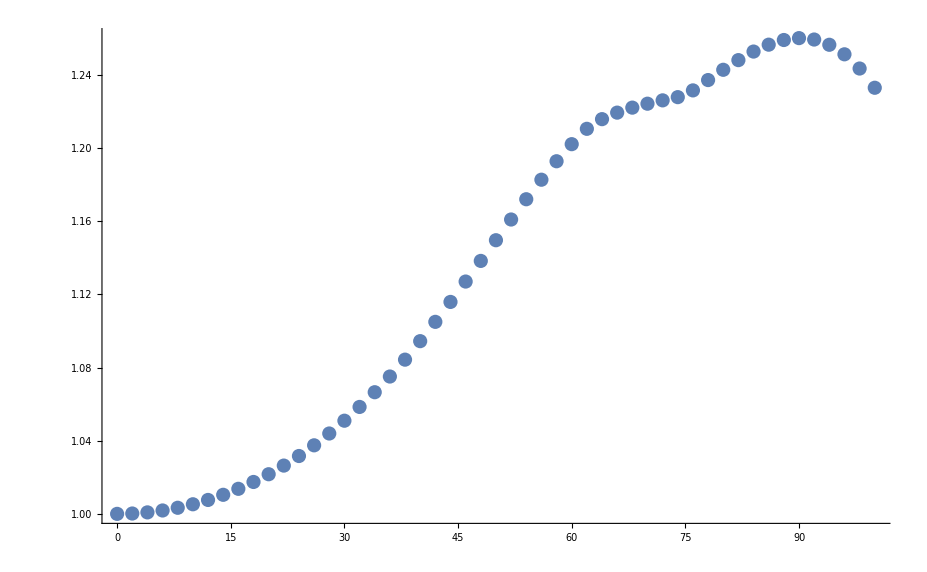

```mathematica
{ListPlot[confinal]}
```